# QNM Poschl-Teller potential cut, three regions

# Grid points

```mathematica
Clear["Global`*"]
SetDirectory[NotebookDirectory[]];
Prec=16 MachinePrecision;
a=Tanh[-1];
b=Tanh[1];
Nz=40;
NzHigh=2 Nz;
z0=a;
z1=b;
Δz=z1-z0;
xf[i_,Nz_]:=Cos[(π i)/Nz];
xtot=N[Table[xf[i,Nz],{i,0,Nz}],Prec ];
xx=N[Table[z0+1/2 Δz (1+xf[i,Nz]),{i,0,Nz}],Prec ];
z0=-1;
z1=a;
Δz=z1-z0;
y1f[i_,Nz_]:=Cos[(2 π i)/(2 Nz +1)];
yy1=N[Table[z0+1/2 Δz (1+y1f[i,Nz]),{i,0,Nz}],Prec ];
z0=b;
z1=1;
Δz=z1-z0;
y2f[i_,Nz_]:=- Cos[(2 π i)/(2 Nz +1)];
yy2=N[Table[z0+1/2 Δz (1+y2f[i,Nz]),{i,0,Nz}],Prec ];
```

# Lobatto differential matrices

```mathematica
Id=IdentityMatrix[Nz+1];
Zero=ConstantArray[0,{Nz+1,Nz+1}];
k[i_,Nz_]:=If[i*(i-Nz)==0, 2,1];
dx1[i_,j_,Nz_]:=If[i≠j,
N[(k[i,Nz]/k[j,Nz])*(-1)^(i-j)/(xf[i, Nz]-xf[j, Nz]), Prec], 0
];
 D1 =N[Table[dx1[i,j,Nz], {i,0,Nz}, {j,0,Nz}] ,Prec  ];

For[i=2, i≤Nz, i++,
D1[[i,i]]= N[-xf[i-1, Nz]/(2*(1-xf[i-1, Nz]^2)),Prec  ];
];
D1[[1,1]]=N[(2 *(Nz)^2+1)/6 , Prec ];
D1[[Nz +1, Nz +1]]=N[-(2 *(Nz)^2+1)/6 , Prec];

dx2[i_,j_,Nz_]:=If[i≠j && i ≠ 0 && i ≠ Nz,
N[(((-1)^(i-j))/k[j,Nz])*((xf[i, Nz])^2+xf[i, Nz]*xf[j, Nz]-2)/((1-(xf[i, Nz])^2)*(xf[j, Nz] - xf[i, Nz])^2), Prec]
,0
];
dx20[j_,Nz_]:= If[j ≠ 0,
N[((2/3)*(-1)^(j)/k[j, Nz])*((2*(Nz)^2+1)*(1-xf[j, Nz])-6)/(1-xf[j, Nz])^2 ,Prec ]
, Unevaluated[Sequence[]]
];
dx2N[j_,Nz_]:= If[j ≠Nz,
 N[((2/3)*(-1)^(Nz + j)/k[j, Nz])*((2*(Nz)^2+1)*(1+xf[j, Nz])-6)/(1+xf[j, Nz])^2 ,Prec ]
, Unevaluated[Sequence[]]
];
D2 =N[Table[dx2[i,j,Nz], {i,0,Nz }, {j,0,Nz}] ,Prec  ];
For[j=2, j≤Nz+1, j++,
D2[[1,j]]= dx20[j-1, Nz];
];
For[j=1, j≤Nz, j++,
D2[[Nz +1,j]]= dx2N[j-1, Nz];
];

For[i=2, i≤Nz, i++,
D2[[i,i]]= N[(-1/(1-(xf[i-1, Nz])^2)^2) -(Nz^2 -1)/(3*(1-xf[i-1, Nz]^2)),Prec  ];
];
D2[[1,1]]=N[((Nz)^4-1)/15 ,Prec ];
D2[[Nz +1, Nz +1]]= N[((Nz)^4-1)/15, Prec  ];
```

# Left & Right Radau differentiation matrices

```mathematica
dy1[i_,j_,Nz_]:=If[i≠j && i ≠ 0 && j ≠ 0,
N[(((-1)^(i-j))/(y1f[i, Nz]-y1f[j, Nz]))*N[Sqrt[(1+y1f[j, Nz])/(1+y1f[i, Nz])] ,Prec  ] ,Prec ],0
];
 dy10[j_,Nz_]:= If[j ≠ 0,
N[  (((-1)^(j))*Sqrt[2*(y1f[j,Nz]+1)]/(-y1f[j, Nz]+1)) ,Prec ]
, Unevaluated[Sequence[]]
];
dy1N[i_,Nz_]:= If[i≠0,
N[ ((-1)^(i+1))/(Sqrt[2]*Sqrt[ y1f[i, Nz]+1]*(-y1f[i, Nz]+1))  ,Prec ]
, Unevaluated[Sequence[]]
];
 Dy11 =N[Table[dy1[i,j,Nz], {i,0,Nz }, {j,0,Nz}] ,Prec  ];
For[j=2, j≤Nz+1, j++,
Dy11[[1,j]]= dy10[j-1, Nz];
];
For[i=2, i≤Nz +1, i++,
Dy11[[i,1]]= dy1N[i-1, Nz];
];

For[i=2, i≤Nz+1, i++,
Dy11[[i,i]]= N[-1/(2*(1-y1f[i-1, Nz]^2)),Prec  ];
];
Dy11[[1,1]]=N[Nz*(Nz +1)/3 ,Prec ];
dy12[i_,j_,Nz_]:=If[i≠j && i ≠ 0 && j ≠ 0,
N[((-1)^(i-j))*(2*(y1f[i, Nz])^2-y1f[i, Nz]+y1f[j, Nz]-2)/(((y1f[i, Nz]-y1f[j, Nz])^2)*(1-(y1f[i, Nz])^2))*Sqrt[(1+y1f[j, Nz])/(1+y1f[i, Nz])] ,Prec  ] ,0

];
 dy120[j_,Nz_]:= If[j ≠ 0,
N[  ((((-1)^(j))*2*Sqrt[2] *Sqrt[1+ y1f[j, Nz]])/(3*(-y1f[j, Nz]+1)^2))* (Nz *(Nz +1)*(1 - y1f[j, Nz])-3) ,Prec ]
, Unevaluated[Sequence[]]
];
dy12N[i_,Nz_]:= If[i≠0,
N[ ((-1)^(i+1))*(2*y1f[i, Nz] +1)/(Sqrt[2]*( y1f[i, Nz]+1)^(3/2)*(-y1f[i, Nz]+1)^2) ,Prec  ]
, Unevaluated[Sequence[]]
];
 Dy12 =N[Table[dy12[i,j,Nz], {i,0,Nz }, {j,0,Nz}] ,Prec  ];
For[j=2, j≤Nz+1, j++,
Dy12[[1,j]]= dy120[j-1, Nz];
];
For[i=2, i≤Nz +1, i++,
Dy12[[i,1]]= dy12N[i-1, Nz];
];

For[i=2, i≤Nz+1, i++,
Dy12[[i,i]]= N[(-Nz*(Nz +1)/(3*(1-(y1f[i-1, Nz])^2))) - (y1f[i-1, Nz]/(1-y1f[i-1, Nz]^2)^2) ,Prec ];
];

Dy12[[1,1]]=N[(Nz -1)*Nz*(Nz +1)*(Nz+2)/15 ,Prec ];
```

# Adapted matrices to three regions

```mathematica
Dy21=-Dy11;
Dy22 = Dy12;
Dy221=N[(2/(1-b))*Dy21 ,Prec ];
Dy222=N[((2/(1-b))^2)*Dy22 ,Prec ];

yy1=Reverse[yy1];
xx=Reverse[xx];
xtot=Reverse[xtot];
D1=Reverse[Reverse[D1,2],1];
D2=Reverse[Reverse[D2,2],1];

Dy111=N[(2/(a+1))*Dy11 ,Prec  ];
Dy112=N[((2/(a+1))^2)*Dy12 ,Prec ];
Dx1=N[(2/(b-a))*D1 ,Prec ];
Dx2=N[((2/(b-a))^2)*D2 ,Prec ];
Dy111=Reverse[Reverse[Dy111,2],1];
Dy112=Reverse[Reverse[Dy112,2],1];
```

# Eigenvalue problem matrices

```mathematica
L1xt=(1-xtot^2)*D2 - 2*xtot*D1-Id;
L2xt= -(2*xtot*D1+Id);

Mxt=ArrayFlatten[{
{Zero,Id} , 
{L1xt,L2xt} }];


L1x=(1-xx^2)*Dx2 - 2*xx*Dx1-Id;
L2x= -(2*xx*Dx1+Id);

Mx=ArrayFlatten[{
{Zero,Id} , 
{L1x,L2x} }];

X1=Id;
Bx=ArrayFlatten[{
{Id, Zero} , 
{Zero,X1 } }];


L1y1=(1-yy1^2)*Dy112 - 2*yy1*Dy111;
L2y1= -(2*yy1*Dy111+Id);

My1=ArrayFlatten[{
{Zero,Id} , 
{L1y1,L2y1} }];
Y1=Id;
By1=ArrayFlatten[{
{Id, Zero} , 
{Zero, Y1 } }];

L1y2=(1-yy2^2)*Dy222 - 2*yy2*Dy221;
L2y2= -(2*yy2*Dy221+Id);

My2=ArrayFlatten[{
{Zero,Id} , 
{L1y2,L2y2} }];

Y2=Id;
By2=ArrayFlatten[{
{Id, Zero} , 
{Zero, Y2 } }];



Id2=IdentityMatrix[2*Nz+2];
Zero2=ConstantArray[0,{2*Nz+2,2*Nz+2}];

M=ArrayFlatten[{
{My1, Zero2, Zero2} ,  
{Zero2, Mx, Zero2} ,
{Zero2, Zero2, My2} }];


B=ArrayFlatten[{
{By1, Zero2, Zero2} ,  
{Zero2, Bx, Zero2} ,
{Zero2, Zero2, By2} }];

Zero6= ConstantArray[0,{6*Nz+6,6*Nz+6}];
Z6=Zero6[[1]];
M[[Nz+1]]= Z6;
B[[Nz+1]]= Z6;
M[[Nz+1, Nz+1]]= -1;
M[[Nz+1, 2*Nz+3]]= 1;

B[[3*Nz+3]]= Z6;
M[[3*Nz+3]]= Z6;
M[[3*Nz+3, 3*Nz+3]]=-1; 
M[[3*Nz+3, 4*Nz+5]]= 1;


Z=Zero[[1]];
M[[2*Nz+3]]=Join[Dy111[[Nz+1]], Z,-Dx1[[1]], Z, Z, Z];
B[[2*Nz+3]]= Z6;
M[[4*Nz+5]]=Join[Z, Z, Dx1[[Nz+1]], Z, - Dy221[[1]], Z];
B[[4*Nz+5]]= Z6;
```

# Solve Eigenvalue problem

```mathematica
EigenSol=Eigenvalues[N[{M, B},Prec]];
EigenSol = -I*EigenSol;
```

```mathematica
Ef=ConstantArray[0,25];
```

```mathematica
s=1;
For[i=1, i≤36, i++,
If[Re@Ec[[i]] ≥ 0.001 || Re@Ec[[i]] < -0.001,
Ec0[[s]]=Ec[[i]];s=s+1, Unevaluated];
];
s
```

13

```mathematica
s=1;
For[i=0, i≤ 2*Nz+2, i++,
If[Re@EVtot[[i]] ≥ -10 && Re@EVtot[[i]] < 10 && Im@EVtot[[i]]  ≥ 0 && Im@EVtot[[i]] < 12,
Ef[[s]]=EVtot[[i]];s=s+1, Unevaluated];
];
s
```

```mathematica
E2=Eigenvalues[N[Mxt,Prec]];
```

```mathematica
E2 = -I*E2;
```

# Graphics, figures...

```mathematica
p=ListPlot[{Re[#],Im[#]}&/@EigenSol,AxesOrigin->{0,0},PlotRange->{{-10,10},{0,12}},ImagePadding->40,AspectRatio->1,Frame->True,
FrameLabel->{{ToExpression["\\mathrm{Im}(\\omega_n)", TeXForm, HoldForm],None},{ToExpression["\\mathrm{Re}(\\omega_n)", TeXForm, HoldForm],None}}, 
PlotStyle->Directive[Blue,PointSize[.015]]
];
```

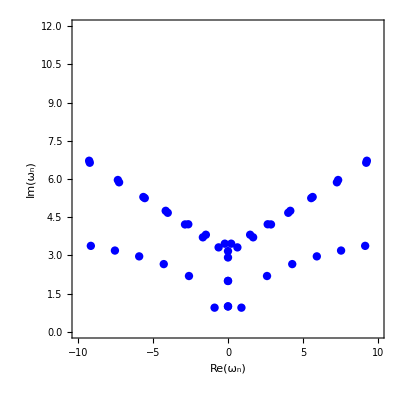

```mathematica
Show[p]
```

```mathematica
E16=EigenSol;
```

```mathematica
p=ListPlot[{Re[#],Im[#]}&/@data,AxesOrigin->{0,0},PlotRange->{{-10,10},{0,12}},ImagePadding->40,AspectRatio->1,Frame->True,
FrameLabel->{{ToExpression["\\mathrm{Im}(\\omega_n)", TeXForm, HoldForm],None},{ToExpression["\\mathrm{Re}(\\omega_n)", TeXForm, HoldForm],None}}, 
PlotStyle->Directive[Blue,PointSize[.015]]
];

p3=ListPlot[{{Re[#],Im[#]}&/@data2, {Re[#],Im[#]}&/@data},AxesOrigin->{0,0},PlotRange->{{-10,10},{0,12}},
ImagePadding->40,AspectRatio->1,Frame->True,FrameLabel->{{ToExpression["\\mathrm{Im}(\\omega_n)", TeXForm, HoldForm],None},
{ToExpression["\\mathrm{Re}(\\omega_n)", TeXForm, HoldForm],None}}, PlotStyle->{Red,Blue, PointSize[.007]},PlotMarkers->Automatic 
 ];


p2=ListPlot[{Re[#],Im[#]}&/@data2,AxesOrigin->{0,0},PlotRange->{{-10,10},{0,12}},   
ImagePadding->40,AspectRatio->1,Frame->True,FrameLabel->{{ToExpression["\\mathrm{Im}(\\omega_n)", TeXForm, HoldForm],None},
{ToExpression["\\mathrm{Re}(\\omega_n)", TeXForm, HoldForm],None}},
PlotStyle->Directive[Red,PointSize[.015]] 
 ];



Show[p3]
```

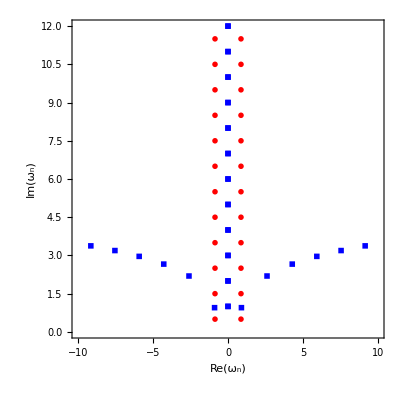

```mathematica
p3=ListPlot[{{Re[#],Im[#]}&/@data2, {Re[#],Im[#]}&/@data},AxesOrigin->{0,0}, PlotRange->{{-10,10},{0,12}},
ImagePadding->40,AspectRatio->1,Frame->True,FrameLabel->{{ToExpression["\\mathrm{Im}(\\omega_n)", TeXForm, HoldForm],None}, 
{ToExpression["\\mathrm{Re}(\\omega_n)", TeXForm, HoldForm],None}},  RotateLabel->True, PlotMarkers->{{•,9},{■,2}} , 
PlotStyle->{Red,Blue}, Axes->False
 ]
```

```mathematica
Show[p3]
```

```mathematica
yyy1=Table[yy1[[k]],{k,1,200,1}];
```

```mathematica
spaceh=Join[yyy1,xx, yy2];
Length[spaceh]
```

602

```mathematica
Vtildy1=ConstantArray[0,200];
Vtildx=(1-xx^2)*ConstantArray[1,201];
Vtildy2=ConstantArray[0,201];
Vtild = Join[Vtildy1,  Vtildx,  Vtildy2];
```

```mathematica
VpT=(1-spaceh^2)*ConstantArray[1,602];
```

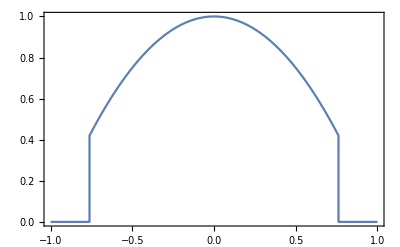

```mathematica
ListLinePlot[Table[{spaceh[[k]],Vtild[[k]]},{k,1,602,1}],Frame->True,Axes->True]
```

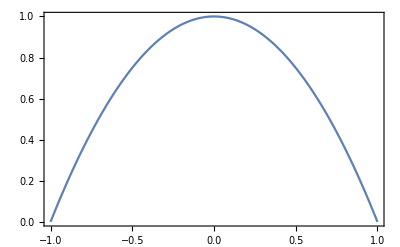

```mathematica
ListLinePlot[Table[{spaceh[[k]],VpT[[k]]},{k,1,602,1}],Frame->True,Axes->True]
```

```mathematica
Vtildy1=ConstantArray[0,200];
Vtildx=N[Table[1-(xx[[i]])^2, {i,1,Nz +1}] ,Prec  ];
Vtildy2=ConstantArray[0,201];
Vtild = Join[Vtildy1,  Vtildx,  Vtildy2];
space=N[Table[ArcTanh[spaceh[[i]]], {i,1,602 }] ,Prec  ];
```

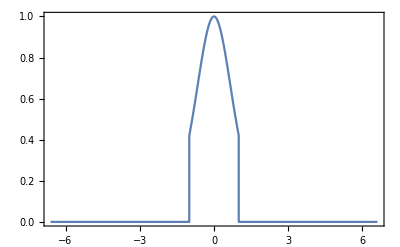

```mathematica
ListLinePlot[Table[{space[[k]],Vtild[[k]]},{k,1,602,1}],Frame->True,Axes->True]
```

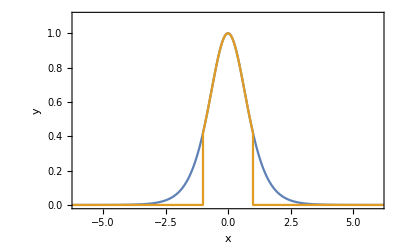
-Graphics-xPotential

```mathematica
Labeled[ListLinePlot[{Table[{space[[k]],VpT[[k]]},{k,1,602,1}],Table[{space[[k]],Vtild[[k]]},{k,1,602,1}]},Frame->True,Axes->True, AxesLabel->{"x","y"}, PlotRange->{{-6,6},{0,1.1}}],{"x","Potential"},{Bottom,Left}]
```

```mathematica
N[ArcTanh[0.76], Prec]
```

0.996215

```mathematica
Vtildy1= N[Table[1-(yy1[[i]])^2, {i,0,Nz }] ,Prec  ];
Vtildx=N[Table[1-(xx[[i]])^2, {i,0,Nz }] ,Prec  ];
Vtildy2=N[Table[1-(yy2[[i]])^2, {i,0,Nz }] ,Prec  ];
Vtild = Join[Vtildy1,  Vtildx,  Vtildy2];
space=Vtildx=N[Table[ArcTanh[spaceh[[i]]], {i,0,603 }] ,Prec  ];
```

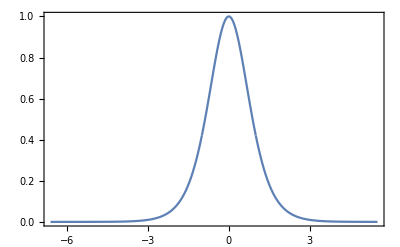

```mathematica
ListLinePlot[Table[{space[[k]],Vtild[[k]]},{k,1,603,1}],Frame->True,Axes->True]
```

```mathematica
Export["test.dat",data2,"Package"]
```

test.dat

```mathematica
test.dat
```

test.dat

```mathematica
Export["PTest.dat",exdata,"Table"];
Print["Done"];
```

Done

```mathematica
c1=Table[Re@Ec0[[iqnm]],{iqnm,1,13}];
```

```mathematica
c2=Table[Im@E11[[iqnm]],{iqnm,1,36}];
```

```mathematica
So=Table[{S1[[iqnm]],S2[[iqnm]]},{iqnm,1,Length[S1]}];
fn="L.dat";
Export[fn,N[So,Prec],"Table"];
Print["Done"];
```

Done

```mathematica
p1=Table[Re@Ef[[iqnm]],{iqnm,1,25}];
```

```mathematica
p2=Table[Im@Ef[[iqnm]],{iqnm,1,25}];
```

```mathematica
po=Table[{p1[[iqnm]],p2[[iqnm]]},{iqnm,1,Length[p1]}];
fn="PT_f.dat";
Export[fn,N[po,Prec],"Table"];
Print["Done"];
```

Done

```mathematica
Table[{Re@EigenSol[[iqnm]],Im@EigenSol[[iqnm]]},{iqnm,5,Length[EigenSol]}]
```